```mathematica
rawData0=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41789674_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData1=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41401021_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData2=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41768161_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData6=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41846559_"<>ToString[i]<>".out"}]],{i,1,100}];(*未开*)
```

```mathematica
rawData3=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41797115_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData4=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41804148_"<>ToString[i]<>".out"}]],{i,1,100}];
rawData5=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/41826931_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData7=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/43222581_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData9=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/43328841_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
rawData8=Table[Quiet@Import[FileNameJoin[{NotebookDirectory[],"results/43306677_"<>ToString[i]<>".out"}]],{i,1,100}];
```

```mathematica
normalize[data_,n_]:=DeleteCases[data,Except[{_,_,_Integer}]]/.{a_,b_,d_}:>{a,b,(1-d/n)}//N;
```

```mathematica
IndepData0=Mean[normalize[#,1000]&/@rawData0];
```

```mathematica
IndepData1=Mean[normalize[#,1000]&/@rawData1];
IndepData2=Mean[normalize[#,1000]&/@rawData2];
```

```mathematica
IndepData3=Mean[normalize[#,1000]&/@rawData3];
```

```mathematica
IndepData4=Mean[normalize[#,1000]&/@rawData4];
```

```mathematica
IndepData6=Mean[normalize[#,1000]&/@Drop[rawData6,67]];
```

```mathematica
IndepData7=Mean[normalize[#,1000]&/@rawData7];
IndepData8=Mean[normalize[#,1000]&/@rawData8];
IndepData9=Mean[normalize[#,1000]&/@rawData9];
```

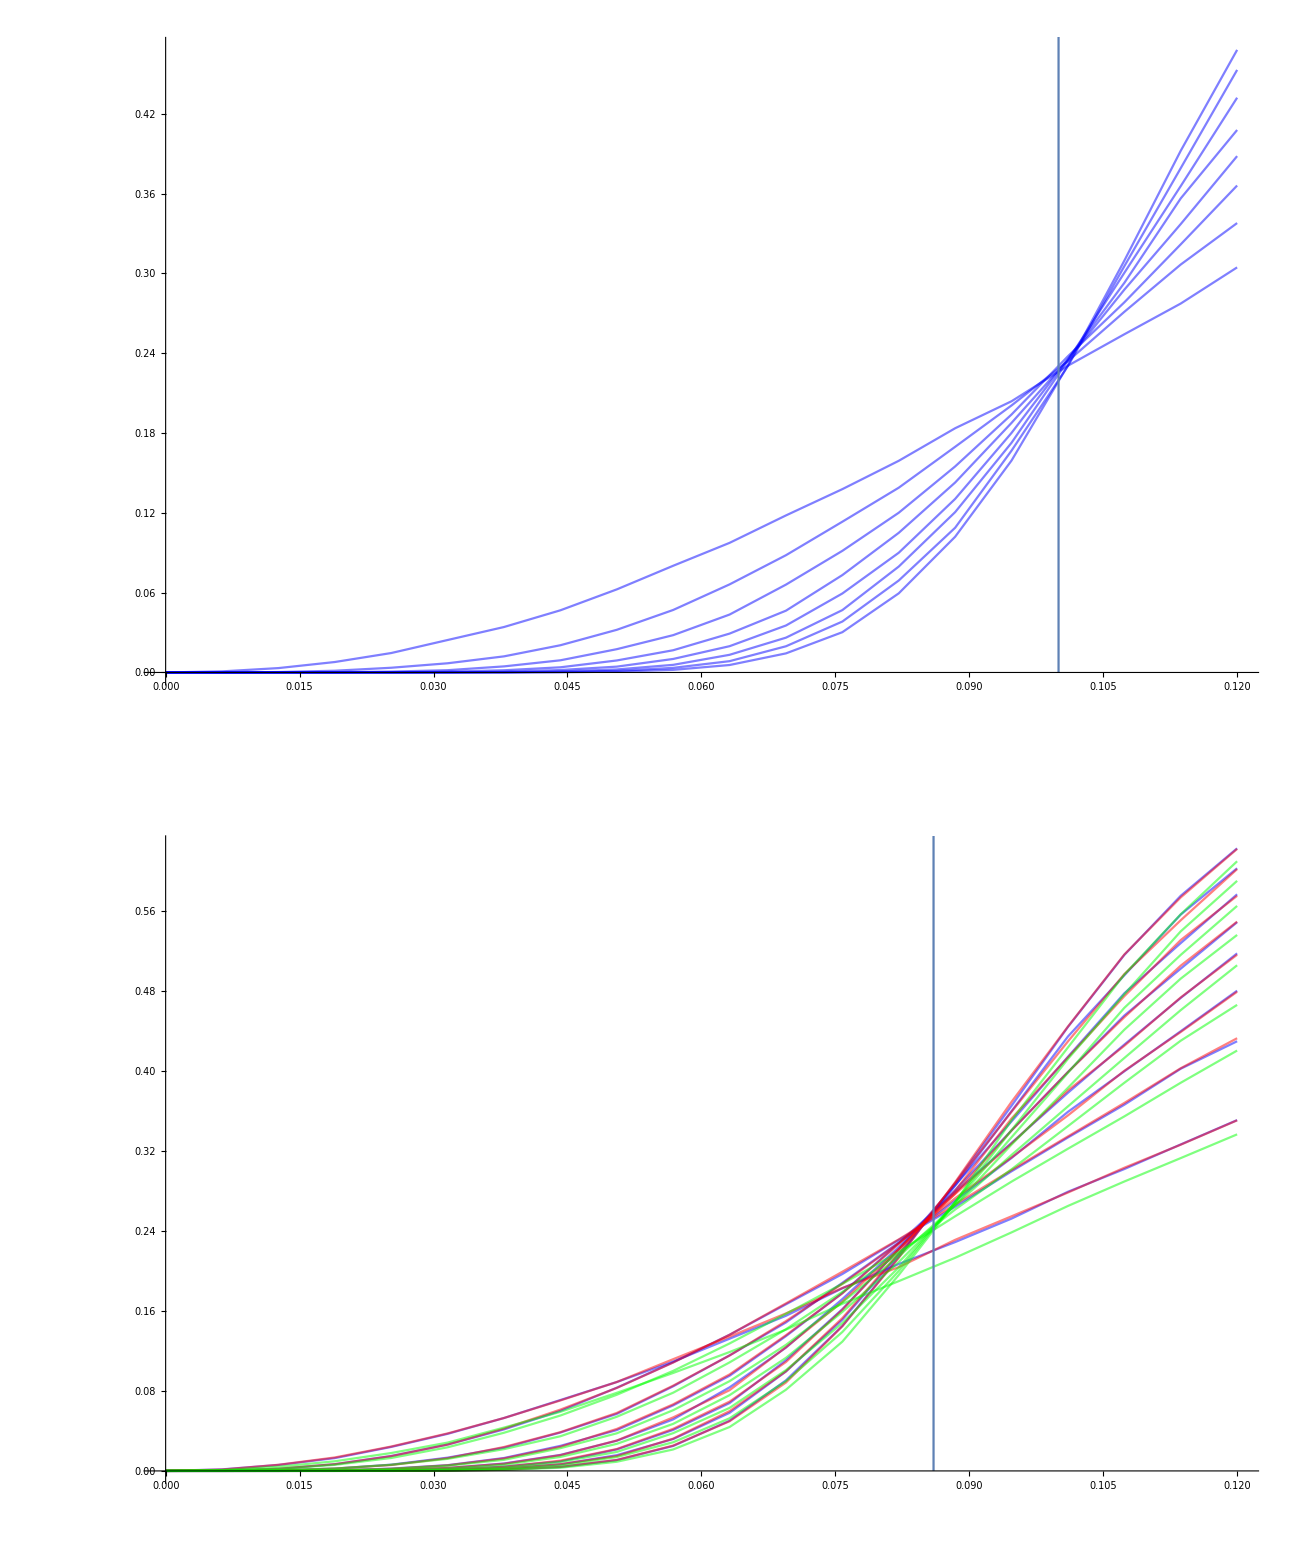

```mathematica
GraphicsColumn[{ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData0,First],{2}],PlotStyle->Directive[Blue,Opacity[0.5]]]~Show~ContourPlot[x==0.1,{x,0,0.12},{y,0,1.02}],ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData9,First],{2}],PlotStyle->Directive[Blue,Opacity[0.5]]]~Show~ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData7,First],{2}],PlotStyle->Directive[Red,Opacity[0.5]]]~Show~ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData8,First],{2}],PlotStyle->Directive[Green,Opacity[0.5]]]~Show~ContourPlot[x==0.086,{x,0,0.8},{y,0,1.02}]}]
```

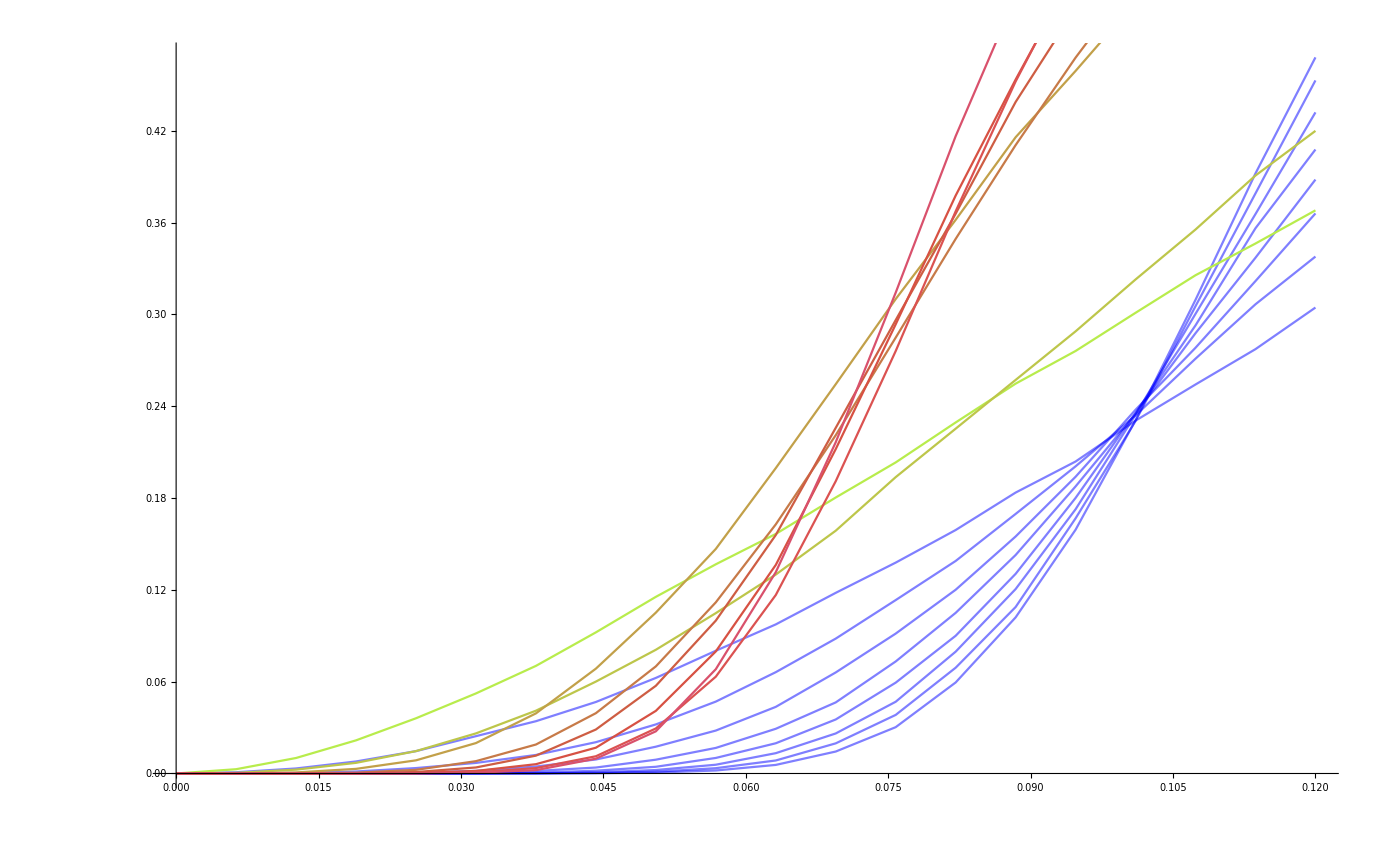

```mathematica
ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData0,First],{2}],PlotStyle->Directive[Blue,Opacity[0.5]]]~Show~ListLinePlot[Map[#[[{2,3}]]&,Values@GroupBy[IndepData7,First],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```

## Model Training

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"5layer_512.txt"}],"Data"];
```

```mathematica
StringLength[]
```

```mathematica
StringDrop[#,-1]&@StringDrop[#,1]&@Flatten[StringCases[#," "~~__~~" "]&@StringCases[#,"loss:"~~__~~"-"]&@DeleteCases[data,x_/;StringLength[x]<3][[1]]]
```

{1.4133}

```mathematica
StringTake[#,{50,70}]&/@DeleteCases[data,x_/;StringLength[x]<4]
```

{loss: 1.4133 - accura,tep - loss: 1.4133 - ,loss: 1.3494 - accura,p - loss: 1.3494 - ac,loss: 1.2892 - accura,p - loss: 1.2892 - ac,loss: 1.2270 - accura,p - loss: 1.2270 - ac,loss: 1.1734 - accura,p - loss: 1.1734 - ac,loss: 1.1158 - accura,p - loss: 1.1158 - ac,loss: 1.0558 - accura,p - loss: 1.0558 - ac,loss: 1.0037 - accura,p - loss: 1.0037 - ac,loss: 0.9612 - accura,p - loss: 0.9612 - ac,loss: 0.9003 - accura,p - loss: 0.9003 - ac,loss: 0.8497 - accura,p - loss: 0.8497 - ac,loss: 0.7977 - accura,p - loss: 0.7977 - ac,loss: 0.7651 - accura,p - loss: 0.7651 - ac,loss: 0.7152 - accura,p - loss: 0.7152 - ac,loss: 0.6681 - accura,p - loss: 0.6681 - ac,loss: 0.6259 - accura,p - loss: 0.6259 - ac,loss: 0.5798 - accura,p - loss: 0.5798 - ac,loss: 0.5379 - accura,p - loss: 0.5379 - ac,loss: 0.5045 - accura,p - loss: 0.5045 - ac,loss: 0.4774 - accura,p - loss: 0.4774 - ac,loss: 0.4449 - accura,p - loss: 0.4449 - ac,loss: 0.4017 - accura,p - loss: 0.4017 - ac,loss: 0.3690 - accura,p - loss: 0.3690 - ac,loss: 0.3561 - accura,p - loss: 0.3561 - ac,loss: 0.3368 - accura,p - loss: 0.3368 - ac,loss: 0.3033 - accura,p - loss: 0.3033 - ac,loss: 0.2793 - accura,p - loss: 0.2793 - ac,loss: 0.2370 - accura,p - loss: 0.2370 - ac,loss: 0.2568 - accura,p - loss: 0.2568 - ac,loss: 0.2375 - accura,p - loss: 0.2375 - ac,loss: 0.1873 - accura,p - loss: 0.1873 - ac,loss: 0.1865 - accura,p - loss: 0.1865 - ac,loss: 0.1589 - accura,p - loss: 0.1589 - ac,loss: 0.1644 - accura,p - loss: 0.1644 - ac,loss: 0.1622 - accura,p - loss: 0.1622 - ac,loss: 0.1426 - accura,p - loss: 0.1426 - ac,loss: 0.1284 - accura,p - loss: 0.1284 - ac,loss: 0.1446 - accura,p - loss: 0.1446 - ac,loss: 0.1322 - accura,p - loss: 0.1322 - ac,loss: 0.1079 - accura,p - loss: 0.1079 - ac,loss: 0.1044 - accura,p - loss: 0.1044 - ac,loss: 0.1094 - accura,p - loss: 0.1094 - ac,loss: 0.1146 - accura,p - loss: 0.1146 - ac,loss: 0.0872 - accura,p - loss: 0.0872 - ac,loss: 0.0971 - accura,p - loss: 0.0971 - ac,loss: 0.0674 - accura,p - loss: 0.0674 - ac,loss: 0.0779 - accura,p - loss: 0.0779 - ac,loss: 0.0926 - accura,p - loss: 0.0926 - ac,loss: 0.0817 - accura,p - loss: 0.0817 - ac,loss: 0.0734 - accura,p - loss: 0.0734 - ac,loss: 0.0843 - accura,p - loss: 0.0843 - ac,loss: 0.0591 - accura,p - loss: 0.0591 - ac,loss: 0.0871 - accura,p - loss: 0.0871 - ac,loss: 0.0881 - accura,p - loss: 0.0881 - ac,loss: 0.0747 - accura,p - loss: 0.0747 - ac,loss: 0.0804 - accura,p - loss: 0.0804 - ac,loss: 0.0842 - accura,p - loss: 0.0842 - ac,loss: 0.0701 - accura,p - loss: 0.0701 - ac,loss: 0.0512 - accura,p - loss: 0.0512 - ac,loss: 0.0522 - accura,p - loss: 0.0522 - ac,loss: 0.0705 - accura,p - loss: 0.0705 - ac,loss: 0.0622 - accura,p - loss: 0.0622 - ac,loss: 0.0570 - accura,p - loss: 0.0570 - ac,loss: 0.0705 - accura,p - loss: 0.0705 - ac,loss: 0.0711 - accura,p - loss: 0.0711 - ac,loss: 0.0335 - accura,p - loss: 0.0335 - ac,loss: 0.0479 - accura,p - loss: 0.0479 - ac,loss: 0.0392 - accura,p - loss: 0.0392 - ac,loss: 0.0445 - accura,p - loss: 0.0445 - ac,loss: 0.0343 - accura,p - loss: 0.0343 - ac,loss: 0.0629 - accura,p - loss: 0.0629 - ac,loss: 0.0329 - accura,p - loss: 0.0329 - ac,loss: 0.0631 - accura,p - loss: 0.0631 - ac,loss: 0.0572 - accura,p - loss: 0.0572 - ac,loss: 0.0573 - accura,p - loss: 0.0573 - ac,loss: 0.0395 - accura,p - loss: 0.0395 - ac,loss: 0.0385 - accura,p - loss: 0.0385 - ac,loss: 0.0555 - accura,p - loss: 0.0555 - ac,loss: 0.0353 - accura,p - loss: 0.0353 - ac,loss: 0.0461 - accura,p - loss: 0.0461 - ac,loss: 0.0518 - accura,p - loss: 0.0518 - ac,loss: 0.0450 - accura,p - loss: 0.0450 - ac,loss: 0.0573 - accura,p - loss: 0.0573 - ac,loss: 0.0391 - accura,p - loss: 0.0391 - ac,loss: 0.0543 - accura,p - loss: 0.0543 - ac,loss: 0.0480 - accura,p - loss: 0.0480 - ac,loss: 0.0514 - accura,p - loss: 0.0514 - ac,loss: 0.0341 - accura,p - loss: 0.0341 - ac,loss: 0.0427 - accura,p - loss: 0.0427 - ac,loss: 0.0336 - accura,p - loss: 0.0336 - ac,loss: 0.0438 - accura,p - loss: 0.0438 - ac,loss: 0.0497 - accura,p - loss: 0.0497 - ac,loss: 0.0503 - accura,p - loss: 0.0503 - ac,loss: 0.0252 - accura,p - loss: 0.0252 - ac,loss: 0.0325 - accura,p - loss: 0.0325 - ac,loss: 0.0612 - accura,p - loss: 0.0612 - ac,loss: 0.0312 - accura,p - loss: 0.0312 - ac,loss: 0.0456 - accura,p - loss: 0.0456 - ac,loss: 0.0300 - accura,p - loss: 0.0300 - ac,loss: 0.0384 - accura,p - loss: 0.0384 - ac,loss: 0.0372 - accura,p - loss: 0.0372 - ac,loss: 0.0350 - accura,p - loss: 0.0350 - ac,loss: 0.0399 - accura,p - loss: 0.0399 - ac,loss: 0.0207 - accura,p - loss: 0.0207 - ac,loss: 0.0527 - accura,p - loss: 0.0527 - ac,loss: 0.0144 - accura,p - loss: 0.0144 - ac,loss: 0.0316 - accura,p - loss: 0.0316 - ac,loss: 0.0227 - accura,p - loss: 0.0227 - ac,loss: 0.0216 - accura,p - loss: 0.0216 - ac,loss: 0.0281 - accura,p - loss: 0.0281 - ac,loss: 0.0363 - accura,p - loss: 0.0363 - ac,loss: 0.0267 - accura,p - loss: 0.0267 - ac,loss: 0.0296 - accura,p - loss: 0.0296 - ac,loss: 0.0271 - accura,p - loss: 0.0271 - ac,loss: 0.0275 - accura,p - loss: 0.0275 - ac,loss: 0.0298 - accura,p - loss: 0.0298 - ac,loss: 0.0380 - accura,p - loss: 0.0380 - ac,loss: 0.0500 - accura,p - loss: 0.0500 - ac,loss: 0.0121 - accura,p - loss: 0.0121 - ac,loss: 0.0190 - accura,p - loss: 0.0190 - ac,loss: 0.0151 - accura,p - loss: 0.0151 - ac,loss: 0.0337 - accura,p - loss: 0.0337 - ac,loss: 0.0255 - accura,p - loss: 0.0255 - ac,loss: 0.0142 - accura,p - loss: 0.0142 - ac,loss: 0.0272 - accura,p - loss: 0.0272 - ac,loss: 0.0257 - accura,p - loss: 0.0257 - ac,loss: 0.0250 - accura,p - loss: 0.0250 - ac,loss: 0.0166 - accura,p - loss: 0.0166 - ac,loss: 0.1149 - accura,p - loss: 0.1149 - ac,loss: 0.0214 - accura,p - loss: 0.0214 - ac,loss: 0.0213 - accura,p - loss: 0.0213 - ac,loss: 0.0255 - accura,p - loss: 0.0255 - ac,loss: 0.0350 - accura,p - loss: 0.0350 - ac,loss: 0.0216 - accura,p - loss: 0.0216 - ac,loss: 0.0365 - accura,p - loss: 0.0365 - ac,loss: 0.0158 - accura,p - loss: 0.0158 - ac,loss: 0.0315 - accura,p - loss: 0.0315 - ac,loss: 0.0363 - accura,p - loss: 0.0363 - ac,loss: 0.0171 - accura,p - loss: 0.0171 - ac,loss: 0.0200 - accura,p - loss: 0.0200 - ac,loss: 0.0222 - accura,p - loss: 0.0222 - ac,loss: 0.0244 - accura,p - loss: 0.0244 - ac,loss: 0.0278 - accura,p - loss: 0.0278 - ac,loss: 0.0214 - accura,p - loss: 0.0214 - ac,loss: 0.0229 - accura,p - loss: 0.0229 - ac,loss: 0.0256 - accura,p - loss: 0.0256 - ac,loss: 0.0399 - accura,p - loss: 0.0399 - ac,loss: 0.0218 - accura,p - loss: 0.0218 - ac,loss: 0.0339 - accura,p - loss: 0.0339 - ac,loss: 0.0155 - accura,p - loss: 0.0155 - ac,loss: 0.0365 - accura,p - loss: 0.0365 - ac,loss: 0.0356 - accura,p - loss: 0.0356 - ac,loss: 0.0158 - accura,p - loss: 0.0158 - ac,loss: 0.0213 - accura,p - loss: 0.0213 - ac,loss: 0.0282 - accura,p - loss: 0.0282 - ac,loss: 0.0162 - accura,p - loss: 0.0162 - ac,loss: 0.0154 - accura,p - loss: 0.0154 - ac,loss: 0.0209 - accura,p - loss: 0.0209 - ac,loss: 0.0154 - accura,p - loss: 0.0154 - ac,loss: 0.0138 - accura,p - loss: 0.0138 - ac,loss: 0.0143 - accura,p - loss: 0.0143 - ac,loss: 0.0183 - accura,p - loss: 0.0183 - ac,loss: 0.0255 - accura,p - loss: 0.0255 - ac,loss: 0.0251 - accura,p - loss: 0.0251 - ac,loss: 0.0076 - accura,p - loss: 0.0076 - ac,loss: 0.0217 - accura,p - loss: 0.0217 - ac,loss: 0.0153 - accura,p - loss: 0.0153 - ac,loss: 0.0258 - accura,p - loss: 0.0258 - ac,loss: 0.0214 - accura,p - loss: 0.0214 - ac,loss: 0.0174 - accura,p - loss: 0.0174 - ac,loss: 0.0224 - accura,p - loss: 0.0224 - ac,loss: 0.0284 - accura,p - loss: 0.0284 - ac,loss: 0.0091 - accura,p - loss: 0.0091 - ac,loss: 0.0246 - accura,p - loss: 0.0246 - ac,loss: 0.0188 - accura,p - loss: 0.0188 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 0.0187 - accura,p - loss: 0.0187 - ac,loss: 0.0091 - accura,p - loss: 0.0091 - ac,loss: 0.0147 - accura,p - loss: 0.0147 - ac,loss: 0.0173 - accura,p - loss: 0.0173 - ac,loss: 0.0092 - accura,p - loss: 0.0092 - ac,loss: 0.0262 - accura,p - loss: 0.0262 - ac,loss: 0.0103 - accura,p - loss: 0.0103 - ac,loss: 0.0106 - accura,p - loss: 0.0106 - ac,loss: 0.0120 - accura,p - loss: 0.0120 - ac,loss: 0.0226 - accura,p - loss: 0.0226 - ac,loss: 0.0403 - accura,p - loss: 0.0403 - ac,loss: 0.0173 - accura,p - loss: 0.0173 - ac,loss: 0.0153 - accura,p - loss: 0.0153 - ac,loss: 0.0176 - accura,p - loss: 0.0176 - ac,loss: 0.0197 - accura,p - loss: 0.0197 - ac,loss: 0.0148 - accura,p - loss: 0.0148 - ac,loss: 0.0161 - accura,p - loss: 0.0161 - ac,loss: 0.0151 - accura,p - loss: 0.0151 - ac,loss: 0.0075 - accura,p - loss: 0.0075 - ac,loss: 0.0161 - accura,p - loss: 0.0161 - ac,loss: 0.0133 - accura,p - loss: 0.0133 - ac,loss: 0.0091 - accura,p - loss: 0.0091 - ac,loss: 0.0236 - accura,p - loss: 0.0236 - ac,loss: 0.0087 - accura,p - loss: 0.0087 - ac,loss: 0.0119 - accura,p - loss: 0.0119 - ac,loss: 0.0084 - accura,p - loss: 0.0084 - ac,loss: 0.0130 - accura,p - loss: 0.0130 - ac,loss: 0.0113 - accura,p - loss: 0.0113 - ac,loss: 0.0292 - accura,p - loss: 0.0292 - ac,loss: 0.0180 - accura,p - loss: 0.0180 - ac,loss: 0.0134 - accura,p - loss: 0.0134 - ac,loss: 0.0344 - accura,p - loss: 0.0344 - ac,loss: 0.0165 - accura,p - loss: 0.0165 - ac,loss: 0.0232 - accura,p - loss: 0.0232 - ac,loss: 0.0125 - accura,p - loss: 0.0125 - ac,loss: 0.0239 - accura,p - loss: 0.0239 - ac,loss: 0.0152 - accura,p - loss: 0.0152 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 0.0217 - accura,p - loss: 0.0217 - ac,loss: 0.0083 - accura,p - loss: 0.0083 - ac,loss: 0.0119 - accura,p - loss: 0.0119 - ac,loss: 0.0135 - accura,p - loss: 0.0135 - ac,loss: 0.0127 - accura,p - loss: 0.0127 - ac,loss: 0.0131 - accura,p - loss: 0.0131 - ac,loss: 0.0060 - accura,p - loss: 0.0060 - ac,loss: 0.0070 - accura,p - loss: 0.0070 - ac,loss: 0.0132 - accura,p - loss: 0.0132 - ac,loss: 0.0070 - accura,p - loss: 0.0070 - ac,loss: 0.0142 - accura,p - loss: 0.0142 - ac,loss: 0.0068 - accura,p - loss: 0.0068 - ac,loss: 0.0102 - accura,p - loss: 0.0102 - ac,loss: 0.0071 - accura,p - loss: 0.0071 - ac,loss: 0.0073 - accura,p - loss: 0.0073 - ac,loss: 0.0062 - accura,p - loss: 0.0062 - ac,loss: 0.0072 - accura,p - loss: 0.0072 - ac,loss: 0.0120 - accura,p - loss: 0.0120 - ac,loss: 0.0114 - accura,p - loss: 0.0114 - ac,loss: 0.0108 - accura,p - loss: 0.0108 - ac,loss: 0.0151 - accura,p - loss: 0.0151 - ac,loss: 0.0166 - accura,p - loss: 0.0166 - ac,loss: 0.0098 - accura,p - loss: 0.0098 - ac,loss: 0.0161 - accura,p - loss: 0.0161 - ac,loss: 0.0061 - accura,p - loss: 0.0061 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 0.0061 - accura,p - loss: 0.0061 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 0.0078 - accura,p - loss: 0.0078 - ac,loss: 0.0136 - accura,p - loss: 0.0136 - ac,loss: 0.0188 - accura,p - loss: 0.0188 - ac,loss: 0.0069 - accura,p - loss: 0.0069 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0066 - accura,p - loss: 0.0066 - ac,loss: 0.0055 - accura,p - loss: 0.0055 - ac,loss: 0.0083 - accura,p - loss: 0.0083 - ac,loss: 0.0063 - accura,p - loss: 0.0063 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0080 - accura,p - loss: 0.0080 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0091 - accura,p - loss: 0.0091 - ac,loss: 0.0171 - accura,p - loss: 0.0171 - ac,loss: 0.0096 - accura,p - loss: 0.0096 - ac,loss: 0.0116 - accura,p - loss: 0.0116 - ac,loss: 0.0163 - accura,p - loss: 0.0163 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0119 - accura,p - loss: 0.0119 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0048 - accura,p - loss: 0.0048 - ac,loss: 0.0042 - accura,p - loss: 0.0042 - ac,loss: 0.0076 - accura,p - loss: 0.0076 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0119 - accura,p - loss: 0.0119 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 0.0120 - accura,p - loss: 0.0120 - ac,loss: 0.0246 - accura,p - loss: 0.0246 - ac,loss: 0.0158 - accura,p - loss: 0.0158 - ac,loss: 0.0069 - accura,p - loss: 0.0069 - ac,loss: 0.0056 - accura,p - loss: 0.0056 - ac,loss: 0.0048 - accura,p - loss: 0.0048 - ac,loss: 0.0041 - accura,p - loss: 0.0041 - ac,loss: 0.0190 - accura,p - loss: 0.0190 - ac,loss: 0.0043 - accura,p - loss: 0.0043 - ac,loss: 0.0075 - accura,p - loss: 0.0075 - ac,loss: 0.0082 - accura,p - loss: 0.0082 - ac,loss: 0.0133 - accura,p - loss: 0.0133 - ac,loss: 0.0064 - accura,p - loss: 0.0064 - ac,loss: 0.0069 - accura,p - loss: 0.0069 - ac,loss: 0.0104 - accura,p - loss: 0.0104 - ac,loss: 0.0076 - accura,p - loss: 0.0076 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0199 - accura,p - loss: 0.0199 - ac,loss: 0.0064 - accura,p - loss: 0.0064 - ac,loss: 0.0060 - accura,p - loss: 0.0060 - ac,loss: 0.0073 - accura,p - loss: 0.0073 - ac,loss: 0.0040 - accura,p - loss: 0.0040 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0062 - accura,p - loss: 0.0062 - ac,loss: 0.0038 - accura,p - loss: 0.0038 - ac,loss: 0.0132 - accura,p - loss: 0.0132 - ac,loss: 0.0110 - accura,p - loss: 0.0110 - ac,loss: 0.0072 - accura,p - loss: 0.0072 - ac,loss: 0.0085 - accura,p - loss: 0.0085 - ac,loss: 0.0039 - accura,p - loss: 0.0039 - ac,loss: 0.0180 - accura,p - loss: 0.0180 - ac,loss: 0.0043 - accura,p - loss: 0.0043 - ac,loss: 0.0040 - accura,p - loss: 0.0040 - ac,loss: 0.0077 - accura,p - loss: 0.0077 - ac,loss: 0.0064 - accura,p - loss: 0.0064 - ac,loss: 0.0038 - accura,p - loss: 0.0038 - ac,loss: 0.0039 - accura,p - loss: 0.0039 - ac,loss: 0.0062 - accura,p - loss: 0.0062 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0049 - accura,p - loss: 0.0049 - ac,loss: 0.0088 - accura,p - loss: 0.0088 - ac,loss: 0.0040 - accura,p - loss: 0.0040 - ac,loss: 0.0064 - accura,p - loss: 0.0064 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0041 - accura,p - loss: 0.0041 - ac,loss: 0.0088 - accura,p - loss: 0.0088 - ac,loss: 0.0052 - accura,p - loss: 0.0052 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0057 - accura,p - loss: 0.0057 - ac,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 0.0056 - accura,p - loss: 0.0056 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0057 - accura,p - loss: 0.0057 - ac,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 0.0093 - accura,p - loss: 0.0093 - ac,loss: 0.0053 - accura,p - loss: 0.0053 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0271 - accura,p - loss: 0.0271 - ac,loss: 0.0023 - accura,p - loss: 0.0023 - ac,loss: 0.0141 - accura,p - loss: 0.0141 - ac,loss: 0.0090 - accura,p - loss: 0.0090 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0180 - accura,p - loss: 0.0180 - ac,loss: 0.0144 - accura,p - loss: 0.0144 - ac,loss: 0.0057 - accura,p - loss: 0.0057 - ac,loss: 0.0056 - accura,p - loss: 0.0056 - ac,loss: 0.0064 - accura,p - loss: 0.0064 - ac,loss: 0.0040 - accura,p - loss: 0.0040 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0063 - accura,p - loss: 0.0063 - ac,loss: 0.0082 - accura,p - loss: 0.0082 - ac,loss: 0.0071 - accura,p - loss: 0.0071 - ac,loss: 0.0088 - accura,p - loss: 0.0088 - ac,loss: 0.0036 - accura,p - loss: 0.0036 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0069 - accura,p - loss: 0.0069 - ac,loss: 0.0057 - accura,p - loss: 0.0057 - ac,loss: 0.0055 - accura,p - loss: 0.0055 - ac,loss: 0.0223 - accura,p - loss: 0.0223 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0121 - accura,p - loss: 0.0121 - ac,loss: 0.0040 - accura,p - loss: 0.0040 - ac,loss: 0.0030 - accura,p - loss: 0.0030 - ac,loss: 0.0067 - accura,p - loss: 0.0067 - ac,loss: 0.0107 - accura,p - loss: 0.0107 - ac,loss: 0.0043 - accura,p - loss: 0.0043 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0173 - accura,p - loss: 0.0173 - ac,loss: 0.0099 - accura,p - loss: 0.0099 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0056 - accura,p - loss: 0.0056 - ac,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 0.0055 - accura,p - loss: 0.0055 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0042 - accura,p - loss: 0.0042 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0103 - accura,p - loss: 0.0103 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0144 - accura,p - loss: 0.0144 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0085 - accura,p - loss: 0.0085 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0030 - accura,p - loss: 0.0030 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0036 - accura,p - loss: 0.0036 - ac,loss: 0.0023 - accura,p - loss: 0.0023 - ac,loss: 0.0098 - accura,p - loss: 0.0098 - ac,loss: 0.0044 - accura,p - loss: 0.0044 - ac,loss: 0.0099 - accura,p - loss: 0.0099 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0055 - accura,p - loss: 0.0055 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0146 - accura,p - loss: 0.0146 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0233 - accura,p - loss: 0.0233 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0030 - accura,p - loss: 0.0030 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0052 - accura,p - loss: 0.0052 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0039 - accura,p - loss: 0.0039 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0054 - accura,p - loss: 0.0054 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0057 - accura,p - loss: 0.0057 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0052 - accura,p - loss: 0.0052 - ac,loss: 0.0090 - accura,p - loss: 0.0090 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0052 - accura,p - loss: 0.0052 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0128 - accura,p - loss: 0.0128 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0095 - accura,p - loss: 0.0095 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 0.0094 - accura,p - loss: 0.0094 - ac,loss: 0.0023 - accura,p - loss: 0.0023 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0054 - accura,p - loss: 0.0054 - ac,loss: 0.0104 - accura,p - loss: 0.0104 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0058 - accura,p - loss: 0.0058 - ac,loss: 0.0019 - accura,p - loss: 0.0019 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0092 - accura,p - loss: 0.0092 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0100 - accura,p - loss: 0.0100 - ac,loss: 0.0050 - accura,p - loss: 0.0050 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 0.0019 - accura,p - loss: 0.0019 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0197 - accura,p - loss: 0.0197 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0019 - accura,p - loss: 0.0019 - ac,loss: 0.0019 - accura,p - loss: 0.0019 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0058 - accura,p - loss: 0.0058 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0038 - accura,p - loss: 0.0038 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0095 - accura,p - loss: 0.0095 - ac,loss: 0.0098 - accura,p - loss: 0.0098 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0089 - accura,p - loss: 0.0089 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0095 - accura,p - loss: 0.0095 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0185 - accura,p - loss: 0.0185 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0154 - accura,p - loss: 0.0154 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0043 - accura,p - loss: 0.0043 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0197 - accura,p - loss: 0.0197 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0060 - accura,p - loss: 0.0060 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0089 - accura,p - loss: 0.0089 - ac,loss: 0.0101 - accura,p - loss: 0.0101 - ac,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0030 - accura,p - loss: 0.0030 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0031 - accura,p - loss: 0.0031 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0023 - accura,p - loss: 0.0023 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0083 - accura,p - loss: 0.0083 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0038 - accura,p - loss: 0.0038 - ac,loss: 9.8002e-04 - ac,p - loss: 9.8002e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0130 - accura,p - loss: 0.0130 - ac,loss: 0.0046 - accura,p - loss: 0.0046 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0103 - accura,p - loss: 0.0103 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 8.9855e-04 - ac,p - loss: 8.9855e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 9.7580e-04 - ac,p - loss: 9.7580e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0073 - accura,p - loss: 0.0073 - ac,loss: 0.0427 - accura,p - loss: 0.0427 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0033 - accura,p - loss: 0.0033 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 9.4417e-04 - ac,p - loss: 9.4417e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0036 - accura,p - loss: 0.0036 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0044 - accura,p - loss: 0.0044 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0025 - accura,p - loss: 0.0025 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0085 - accura,p - loss: 0.0085 - ac,loss: 0.0047 - accura,p - loss: 0.0047 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0087 - accura,p - loss: 0.0087 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 9.3899e-04 - ac,p - loss: 9.3899e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0039 - accura,p - loss: 0.0039 - ac,loss: 0.0032 - accura,p - loss: 0.0032 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0229 - accura,p - loss: 0.0229 - ac,loss: 0.0037 - accura,p - loss: 0.0037 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 9.2242e-04 - ac,p - loss: 9.2242e-04 ,loss: 8.8577e-04 - ac,p - loss: 8.8577e-04 ,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 9.5556e-04 - ac,p - loss: 9.5556e-04 ,loss: 9.7693e-04 - ac,p - loss: 9.7693e-04 ,loss: 0.0844 - accura,p - loss: 0.0844 - ac,loss: 0.0130 - accura,p - loss: 0.0130 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 9.3500e-04 - ac,p - loss: 9.3500e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 9.9863e-04 - ac,p - loss: 9.9863e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0084 - accura,p - loss: 0.0084 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 9.1360e-04 - ac,p - loss: 9.1360e-04 ,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 0.0084 - accura,p - loss: 0.0084 - ac,loss: 8.6888e-04 - ac,p - loss: 8.6888e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 9.7960e-04 - ac,p - loss: 9.7960e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 9.3680e-04 - ac,p - loss: 9.3680e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 9.7547e-04 - ac,p - loss: 9.7547e-04 ,loss: 9.0594e-04 - ac,p - loss: 9.0594e-04 ,loss: 0.0098 - accura,p - loss: 0.0098 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 8.4660e-04 - ac,p - loss: 8.4660e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0087 - accura,p - loss: 0.0087 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 9.3746e-04 - ac,p - loss: 9.3746e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 8.7953e-04 - ac,p - loss: 8.7953e-04 ,loss: 9.3528e-04 - ac,p - loss: 9.3528e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 7.5205e-04 - ac,p - loss: 7.5205e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0018 - accura,p - loss: 0.0018 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0035 - accura,p - loss: 0.0035 - ac,loss: 9.8360e-04 - ac,p - loss: 9.8360e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 7.3797e-04 - ac,p - loss: 7.3797e-04 ,loss: 0.0028 - accura,p - loss: 0.0028 - ac,loss: 8.7833e-04 - ac,p - loss: 8.7833e-04 ,loss: 7.7352e-04 - ac,p - loss: 7.7352e-04 ,loss: 0.0100 - accura,p - loss: 0.0100 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 7.8305e-04 - ac,p - loss: 7.8305e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0065 - accura,p - loss: 0.0065 - ac,loss: 0.0094 - accura,p - loss: 0.0094 - ac,loss: 8.4615e-04 - ac,p - loss: 8.4615e-04 ,loss: 0.0034 - accura,p - loss: 0.0034 - ac,loss: 0.0084 - accura,p - loss: 0.0084 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 7.8849e-04 - ac,p - loss: 7.8849e-04 ,loss: 0.0049 - accura,p - loss: 0.0049 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 8.9186e-04 - ac,p - loss: 8.9186e-04 ,loss: 9.1863e-04 - ac,p - loss: 9.1863e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 8.7947e-04 - ac,p - loss: 8.7947e-04 ,loss: 9.6408e-04 - ac,p - loss: 9.6408e-04 ,loss: 8.2405e-04 - ac,p - loss: 8.2405e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 9.7246e-04 - ac,p - loss: 9.7246e-04 ,loss: 9.8427e-04 - ac,p - loss: 9.8427e-04 ,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 8.9217e-04 - ac,p - loss: 8.9217e-04 ,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 9.5576e-04 - ac,p - loss: 9.5576e-04 ,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 8.7438e-04 - ac,p - loss: 8.7438e-04 ,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 7.9239e-04 - ac,p - loss: 7.9239e-04 ,loss: 7.9191e-04 - ac,p - loss: 7.9191e-04 ,loss: 9.9060e-04 - ac,p - loss: 9.9060e-04 ,loss: 8.3081e-04 - ac,p - loss: 8.3081e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 8.2165e-04 - ac,p - loss: 8.2165e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 8.5692e-04 - ac,p - loss: 8.5692e-04 ,loss: 6.7645e-04 - ac,p - loss: 6.7645e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 7.1489e-04 - ac,p - loss: 7.1489e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 7.7831e-04 - ac,p - loss: 7.7831e-04 ,loss: 7.5135e-04 - ac,p - loss: 7.5135e-04 ,loss: 9.5026e-04 - ac,p - loss: 9.5026e-04 ,loss: 8.3063e-04 - ac,p - loss: 8.3063e-04 ,loss: 5.9806e-04 - ac,p - loss: 5.9806e-04 ,loss: 0.0086 - accura,p - loss: 0.0086 - ac,loss: 0.0110 - accura,p - loss: 0.0110 - ac,loss: 7.6659e-04 - ac,p - loss: 7.6659e-04 ,loss: 6.7903e-04 - ac,p - loss: 6.7903e-04 ,loss: 6.6083e-04 - ac,p - loss: 6.6083e-04 ,loss: 7.5447e-04 - ac,p - loss: 7.5447e-04 ,loss: 8.5073e-04 - ac,p - loss: 8.5073e-04 ,loss: 8.6213e-04 - ac,p - loss: 8.6213e-04 ,loss: 0.0076 - accura,p - loss: 0.0076 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 7.6889e-04 - ac,p - loss: 7.6889e-04 ,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 8.4311e-04 - ac,p - loss: 8.4311e-04 ,loss: 5.9692e-04 - ac,p - loss: 5.9692e-04 ,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 8.2121e-04 - ac,p - loss: 8.2121e-04 ,loss: 5.7439e-04 - ac,p - loss: 5.7439e-04 ,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 7.0215e-04 - ac,p - loss: 7.0215e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 7.9228e-04 - ac,p - loss: 7.9228e-04 ,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 6.2172e-04 - ac,p - loss: 6.2172e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 6.8737e-04 - ac,p - loss: 6.8737e-04 ,loss: 7.1106e-04 - ac,p - loss: 7.1106e-04 ,loss: 7.2061e-04 - ac,p - loss: 7.2061e-04 ,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 7.2398e-04 - ac,p - loss: 7.2398e-04 ,loss: 6.7793e-04 - ac,p - loss: 6.7793e-04 ,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0836 - accura,p - loss: 0.0836 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 0.0015 - accura,p - loss: 0.0015 - ac,loss: 6.6364e-04 - ac,p - loss: 6.6364e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 6.8093e-04 - ac,p - loss: 6.8093e-04 ,loss: 5.7957e-04 - ac,p - loss: 5.7957e-04 ,loss: 7.3635e-04 - ac,p - loss: 7.3635e-04 ,loss: 6.7013e-04 - ac,p - loss: 6.7013e-04 ,loss: 5.4564e-04 - ac,p - loss: 5.4564e-04 ,loss: 0.0051 - accura,p - loss: 0.0051 - ac,loss: 7.3383e-04 - ac,p - loss: 7.3383e-04 ,loss: 6.5972e-04 - ac,p - loss: 6.5972e-04 ,loss: 7.1316e-04 - ac,p - loss: 7.1316e-04 ,loss: 6.1194e-04 - ac,p - loss: 6.1194e-04 ,loss: 7.3666e-04 - ac,p - loss: 7.3666e-04 ,loss: 6.3954e-04 - ac,p - loss: 6.3954e-04 ,loss: 5.3354e-04 - ac,p - loss: 5.3354e-04 ,loss: 0.0085 - accura,p - loss: 0.0085 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 0.0112 - accura,p - loss: 0.0112 - ac,loss: 6.9098e-04 - ac,p - loss: 6.9098e-04 ,loss: 0.0090 - accura,p - loss: 0.0090 - ac,loss: 0.0080 - accura,p - loss: 0.0080 - ac,loss: 7.8976e-04 - ac,p - loss: 7.8976e-04 ,loss: 7.4764e-04 - ac,p - loss: 7.4764e-04 ,loss: 7.0694e-04 - ac,p - loss: 7.0694e-04 ,loss: 0.0096 - accura,p - loss: 0.0096 - ac,loss: 0.0023 - accura,p - loss: 0.0023 - ac,loss: 6.5091e-04 - ac,p - loss: 6.5091e-04 ,loss: 7.5336e-04 - ac,p - loss: 7.5336e-04 ,loss: 7.4560e-04 - ac,p - loss: 7.4560e-04 ,loss: 0.0058 - accura,p - loss: 0.0058 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 6.6762e-04 - ac,p - loss: 6.6762e-04 ,loss: 8.1591e-04 - ac,p - loss: 8.1591e-04 ,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 8.3478e-04 - ac,p - loss: 8.3478e-04 ,loss: 6.6845e-04 - ac,p - loss: 6.6845e-04 ,loss: 7.3037e-04 - ac,p - loss: 7.3037e-04 ,loss: 8.9136e-04 - ac,p - loss: 8.9136e-04 ,loss: 6.8493e-04 - ac,p - loss: 6.8493e-04 ,loss: 6.2383e-04 - ac,p - loss: 6.2383e-04 ,loss: 6.8843e-04 - ac,p - loss: 6.8843e-04 ,loss: 0.0214 - accura,p - loss: 0.0214 - ac,loss: 8.2402e-04 - ac,p - loss: 8.2402e-04 ,loss: 7.0248e-04 - ac,p - loss: 7.0248e-04 ,loss: 7.6744e-04 - ac,p - loss: 7.6744e-04 ,loss: 0.0061 - accura,p - loss: 0.0061 - ac,loss: 7.9821e-04 - ac,p - loss: 7.9821e-04 ,loss: 9.7191e-04 - ac,p - loss: 9.7191e-04 ,loss: 0.0080 - accura,p - loss: 0.0080 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 8.1801e-04 - ac,p - loss: 8.1801e-04 ,loss: 8.1926e-04 - ac,p - loss: 8.1926e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 7.5110e-04 - ac,p - loss: 7.5110e-04 ,loss: 7.9206e-04 - ac,p - loss: 7.9206e-04 ,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 8.6076e-04 - ac,p - loss: 8.6076e-04 ,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 6.6713e-04 - ac,p - loss: 6.6713e-04 ,loss: 7.1131e-04 - ac,p - loss: 7.1131e-04 ,loss: 0.0191 - accura,p - loss: 0.0191 - ac,loss: 6.7882e-04 - ac,p - loss: 6.7882e-04 ,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 8.8320e-04 - ac,p - loss: 8.8320e-04 ,loss: 7.9384e-04 - ac,p - loss: 7.9384e-04 ,loss: 7.5560e-04 - ac,p - loss: 7.5560e-04 ,loss: 0.0022 - accura,p - loss: 0.0022 - ac,loss: 7.2015e-04 - ac,p - loss: 7.2015e-04 ,loss: 8.6143e-04 - ac,p - loss: 8.6143e-04 ,loss: 0.0075 - accura,p - loss: 0.0075 - ac,loss: 8.9648e-04 - ac,p - loss: 8.9648e-04 ,loss: 7.2360e-04 - ac,p - loss: 7.2360e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 6.5056e-04 - ac,p - loss: 6.5056e-04 ,loss: 9.7873e-04 - ac,p - loss: 9.7873e-04 ,loss: 7.4798e-04 - ac,p - loss: 7.4798e-04 ,loss: 6.4008e-04 - ac,p - loss: 6.4008e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0179 - accura,p - loss: 0.0179 - ac,loss: 7.9614e-04 - ac,p - loss: 7.9614e-04 ,loss: 6.3714e-04 - ac,p - loss: 6.3714e-04 ,loss: 8.1665e-04 - ac,p - loss: 8.1665e-04 ,loss: 6.9898e-04 - ac,p - loss: 6.9898e-04 ,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 5.2205e-04 - ac,p - loss: 5.2205e-04 ,loss: 5.7514e-04 - ac,p - loss: 5.7514e-04 ,loss: 6.9690e-04 - ac,p - loss: 6.9690e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 7.3253e-04 - ac,p - loss: 7.3253e-04 ,loss: 0.0078 - accura,p - loss: 0.0078 - ac,loss: 9.7209e-04 - ac,p - loss: 9.7209e-04 ,loss: 6.4522e-04 - ac,p - loss: 6.4522e-04 ,loss: 0.0079 - accura,p - loss: 0.0079 - ac,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0086 - accura,p - loss: 0.0086 - ac,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 6.7325e-04 - ac,p - loss: 6.7325e-04 ,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 6.6110e-04 - ac,p - loss: 6.6110e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 8.6206e-04 - ac,p - loss: 8.6206e-04 ,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 0.0016 - accura,p - loss: 0.0016 - ac,loss: 7.0776e-04 - ac,p - loss: 7.0776e-04 ,loss: 0.0010 - accura,p - loss: 0.0010 - ac,loss: 6.1844e-04 - ac,p - loss: 6.1844e-04 ,loss: 6.2449e-04 - ac,p - loss: 6.2449e-04 ,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 6.3296e-04 - ac,p - loss: 6.3296e-04 ,loss: 5.8425e-04 - ac,p - loss: 5.8425e-04 ,loss: 5.4443e-04 - ac,p - loss: 5.4443e-04 ,loss: 5.3127e-04 - ac,p - loss: 5.3127e-04 ,loss: 7.6036e-04 - ac,p - loss: 7.6036e-04 ,loss: 8.0597e-04 - ac,p - loss: 8.0597e-04 ,loss: 6.5222e-04 - ac,p - loss: 6.5222e-04 ,loss: 6.2008e-04 - ac,p - loss: 6.2008e-04 ,loss: 0.0104 - accura,p - loss: 0.0104 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0105 - accura,p - loss: 0.0105 - ac,loss: 0.0024 - accura,p - loss: 0.0024 - ac,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0014 - accura,p - loss: 0.0014 - ac,loss: 6.0100e-04 - ac,p - loss: 6.0100e-04 ,loss: 5.8873e-04 - ac,p - loss: 5.8873e-04 ,loss: 7.0159e-04 - ac,p - loss: 7.0159e-04 ,loss: 4.8725e-04 - ac,p - loss: 4.8725e-04 ,loss: 5.5249e-04 - ac,p - loss: 5.5249e-04 ,loss: 6.3649e-04 - ac,p - loss: 6.3649e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 5.0823e-04 - ac,p - loss: 5.0823e-04 ,loss: 5.6921e-04 - ac,p - loss: 5.6921e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 5.9665e-04 - ac,p - loss: 5.9665e-04 ,loss: 5.7585e-04 - ac,p - loss: 5.7585e-04 ,loss: 6.0227e-04 - ac,p - loss: 6.0227e-04 ,loss: 0.0071 - accura,p - loss: 0.0071 - ac,loss: 9.8035e-04 - ac,p - loss: 9.8035e-04 ,loss: 6.6356e-04 - ac,p - loss: 6.6356e-04 ,loss: 6.4553e-04 - ac,p - loss: 6.4553e-04 ,loss: 5.5958e-04 - ac,p - loss: 5.5958e-04 ,loss: 0.0094 - accura,p - loss: 0.0094 - ac,loss: 5.2082e-04 - ac,p - loss: 5.2082e-04 ,loss: 0.0027 - accura,p - loss: 0.0027 - ac,loss: 0.0068 - accura,p - loss: 0.0068 - ac,loss: 4.8320e-04 - ac,p - loss: 4.8320e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 5.2111e-04 - ac,p - loss: 5.2111e-04 ,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 0.0055 - accura,p - loss: 0.0055 - ac,loss: 5.6201e-04 - ac,p - loss: 5.6201e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 0.0012 - accura,p - loss: 0.0012 - ac,loss: 6.2948e-04 - ac,p - loss: 6.2948e-04 ,loss: 0.0082 - accura,p - loss: 0.0082 - ac,loss: 6.3700e-04 - ac,p - loss: 6.3700e-04 ,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 4.9420e-04 - ac,p - loss: 4.9420e-04 ,loss: 7.8259e-04 - ac,p - loss: 7.8259e-04 ,loss: 0.0029 - accura,p - loss: 0.0029 - ac,loss: 6.3091e-04 - ac,p - loss: 6.3091e-04 ,loss: 5.8409e-04 - ac,p - loss: 5.8409e-04 ,loss: 0.0011 - accura,p - loss: 0.0011 - ac,loss: 5.7817e-04 - ac,p - loss: 5.7817e-04 ,loss: 6.4354e-04 - ac,p - loss: 6.4354e-04 ,loss: 0.0020 - accura,p - loss: 0.0020 - ac,loss: 5.5629e-04 - ac,p - loss: 5.5629e-04 ,loss: 5.8001e-04 - ac,p - loss: 5.8001e-04 ,loss: 9.7827e-04 - ac,p - loss: 9.7827e-04 ,loss: 6.6960e-04 - ac,p - loss: 6.6960e-04 ,loss: 7.1636e-04 - ac,p - loss: 7.1636e-04 ,loss: 0.0017 - accura,p - loss: 0.0017 - ac,loss: 6.7412e-04 - ac,p - loss: 6.7412e-04 ,loss: 6.4645e-04 - ac,p - loss: 6.4645e-04 ,loss: 6.8535e-04 - ac,p - loss: 6.8535e-04 ,loss: 0.0108 - accura,p - loss: 0.0108 - ac,loss: 7.2036e-04 - ac,p - loss: 7.2036e-04 ,loss: 6.1804e-04 - ac,p - loss: 6.1804e-04 ,loss: 6.1148e-04 - ac,p - loss: 6.1148e-04 ,loss: 5.5917e-04 - ac,p - loss: 5.5917e-04 ,loss: 5.1602e-04 - ac,p - loss: 5.1602e-04 ,loss: 0.0013 - accura,p - loss: 0.0013 - ac,loss: 5.5497e-04 - ac,p - loss: 5.5497e-04 ,loss: 5.2962e-04 - ac,p - loss: 5.2962e-04 ,loss: 5.0167e-04 - ac,p - loss: 5.0167e-04 ,loss: 6.6656e-04 - ac,p - loss: 6.6656e-04 ,loss: 6.3483e-04 - ac,p - loss: 6.3483e-04 ,loss: 0.0026 - accura,p - loss: 0.0026 - ac,loss: 5.8218e-04 - ac,p - loss: 5.8218e-04 ,loss: 0.0021 - accura,p - loss: 0.0021 - ac,loss: 5.5642e-04 - ac,p - loss: 5.5642e-04 ,loss: 5.5550e-04 - ac,p - loss: 5.5550e-04 }